# optical resonator stability condition

P. Huft

Derivation from http://www.optique-ingenieur.org/en/courses/OPI_ang_M01_C03/co/Contenu_05.html, but probably exists elsewhere.

Stability condition is 0<= (A+D+2)/4<=1  for A and D the diagonal elements of the round trip matrix for the cavity.

## 0<g1 g2<1 derivation.

```mathematica
Clear[d,R1,R2];
d;(*the one-way distance d is approximately the cavity length L*)
(*R1=2f1;
R2=2f2;*)
M1={{1,0},{-2/R1,1}};
Md={{1,d},{0,1}};
M2={{1,0},{-2/R2,1}};
(*T=M1.Md.M2.Md;*)
T=M1.Md.M2.Md;
cond=(T[[1,1]]+T[[2,2]]+2)/4
cond==(1-d/R1)(1-d/R2)//FullSimplify
```

1/4 (4-(2 d)/R1+d (-2/R1-(2 (1-(2 d)/R1))/R2)-(2 d)/R2)

True

Below, I plot constant values of the stability parameter as a function of the mirror radii normalized to the cavity length. The diagonal line of the small triangle in the lower left corresponds to R2 = d - R1, for which the concentric cavity with R2=R1=d/2 is a special case. The cross region for R1=R2=d is the confocal case, where the stability parameter is 0, and the region to the upper right of this goes from near-confocal to flat mirrors, at which point the cavity would become unstable.

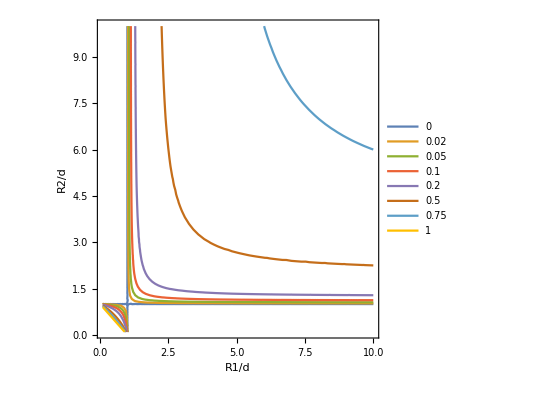

```mathematica
d=1;
stability={0,0.02,0.05,0.1,0.2,0.5,0.75,1};
ContourPlot[Evaluate[Table[cond==i,{i,stability}]],{R1,0.1d,10d},{R2,0.1d,10d},PlotRange->All,PlotLegends->stability,FrameLabel->{"R1/d","R2/d"}]
```

## misaligned cavity

```mathematica
Clear[d,R1,R2];
d;(*the one-way distance d is approximately the cavity length L*)
(*R1=2f1;
R2=2f2;*)
M1={{1,0},{-2/R1,1}};
Md={{1,d},{0,1}};
M2={{1,0},{-2/R2,1}};
(*T=M1.Md.M2.Md;*)
T=M1.Md.M2.Md;
cond=(T[[1,1]]+T[[2,2]]+2)/4
cond==(1-d/R1)(1-d/R2)//FullSimplify
```

1/4 (4-(2 d)/R1+d (-2/R1-(2 (1-(2 d)/R1))/R2)-(2 d)/R2)

True

Below, I plot constant values of the stability parameter as a function of the mirror radii normalized to the cavity length. The diagonal line of the small triangle in the lower left corresponds to R2 = d - R1, for which the concentric cavity with R2=R1=d/2 is a special case. The cross region for R1=R2=d is the confocal case, where the stability parameter is 0, and the region to the upper right of this goes from near-confocal to flat mirrors, at which point the cavity would become unstable.

```mathematica
d=1;
stability={0,0.02,0.05,0.1,0.2,0.5,0.75,1};
ContourPlot[Evaluate[Table[cond==i,{i,stability}]],{R1,0.1d,10d},{R2,0.1d,10d},PlotRange->All,PlotLegends->stability,FrameLabel->{"R1/d","R2/d"}]
```

-Graphics-

```mathematica
D[√(R^2+(x-x0)^2),x]
```

(x-x0)/(√(R^2+(x-x0)^2))

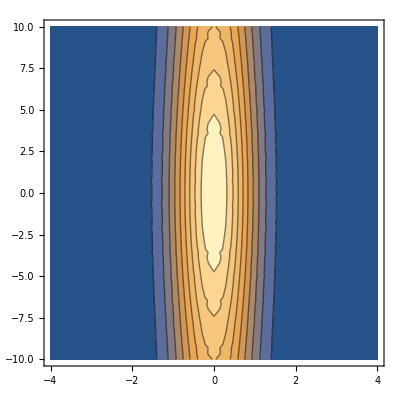

```mathematica
ContourPlot[Exp[-x^2-3] 1/(√(1+(z/10)^2)),{x,-4,4},{z,-10,10}]
```